# Nonlinear fluctuating hydrodynamics for anharmonic chains

Example file for computing the coupling constants in Appendix A of Ref. [1]

Copyright (C) 2013-2014, Christian B. Mendl
All rights reserved.
http://christian.mendl.net

This program is free software; you can redistribute it and/or
modify it under the terms of the Simplified BSD License	
http://www.opensource.org/licenses/bsd-license.php

References
	[1] Herbert Spohn
	Nonlinear fluctuating hydrodynamics for anharmonic chains
	J. Stat. Phys. 154, 1191-1227 (2014), arXiv:1305.6412

	[2] Christian B. Mendl, Herbert Spohn
	Dynamic correlators of Fermi-Pasta-Ulam chains and nonlinear fluctuating hydrodynamics
	Phys. Rev. Lett. 111, 230601 (2013), arXiv:1305.1209

	[3] Christian B. Mendl, Herbert Spohn
	Equilibrium time-correlation functions for one-dimensional hard-point systems
	Phys. Rev. E 90, 012147 (2014), arXiv:1403.0213

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<NFHchains_base.m;
```

## Calculate coupling constants

```mathematica
(* FPU potential with a=2 *)
Subscript[V, val][x_]:=x^2/2+(*a*)2 x^3/3+x^4/4
```

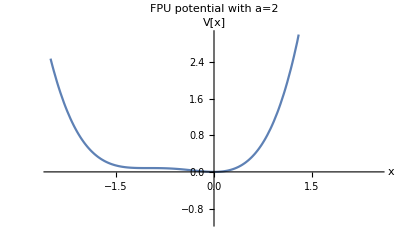

```mathematica
Plot[Subscript[V, val][x],{x,-2.5,2.5},AxesLabel->{"x","V[x]"},PlotLabel->"FPU potential with a=2",
PlotRange->{Automatic,{-1.1,3}}]
```

```mathematica
(* pressure *)
Subscript[p, val]=1;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=2;
```

```mathematica
(* mean length given V[x], p, β *)
ell[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]
```

-1.51696

```mathematica
(* mean energy given V[x], p, β *)
En[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]
```

0.624156

```mathematica
(* matrix A *)
A[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]//MatrixForm
```

(0 | -1 | 0
-1.15429 | 0 | 0.961806
0 | 1 | 0)

```mathematica
(* sound velocity *)
Subscript[c, sound]=csq[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]^(1/2)
```

1.45468

```mathematica
(* "rotation" matrix R *)
R[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]//MatrixForm
```

(-0.7935 | -1. | 0.66118
1.89594 | 0. | 1.89594
-0.7935 | 1. | 0.66118)

```mathematica
(* G coupling matrices *)
```

```mathematica
Subscript[G, 1]=Table[G[1,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, 1]//MatrixForm
```

(-0.24236 | -0.075565 | 0.238543
-0.075565 | -0.0669417 | -0.075565
0.238543 | -0.075565 | 0.238543)

```mathematica
Subscript[G, 0]=Table[G[0,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, 0]//MatrixForm
```

(-0.689497 | 0 | 0.
0 | 0 | 0
0. | 0 | 0.689497)

```mathematica
Subscript[G, -1]=Table[G[-1,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, -1]//MatrixForm
```

(-0.238543 | 0.075565 | -0.238543
0.075565 | 0.0669417 | 0.075565
-0.238543 | 0.075565 | 0.24236)

```mathematica
(* check: Subscript[G, -1] == -AntiTranspose[Subscript[G, 1]] *)
Norm[Subscript[G, -1]+Table[Subscript[G, 1]⟦2-j,2-i⟧,{i,-1,1},{j,-1,1}]]
```

0.

```mathematica
(* symbolic calculation example: Γ determinant *)
Γ[{V,p,β},True]
```

1/(2 β (∫_(-∞)^∞ ⅇ^(-β (p x+V[x]))ⅆx)^3)((∫_(-∞)^∞ ⅇ^(-β (p x+V[x]))ⅆx)^2 ∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) x^2ⅆx-2 β^2 ((∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) x^2ⅆx) (∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) V[x]ⅆx)^2+(∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) xⅆx) (-2 (∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) V[x]ⅆx) ∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) x V[x]ⅆx+(∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) xⅆx) ∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) V[x]^2ⅆx))-(∫_(-∞)^∞ ⅇ^(-β (p x+V[x]))ⅆx) ((∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) xⅆx)^2+2 β^2 ((∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) x V[x]ⅆx)^2-(∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) x^2ⅆx) ∫_(-∞)^∞ ⅇ^(-β (p x+V[x])) V[x]^2ⅆx)))